```mathematica
toDate[dateObject_DateObject] := DateObject[DateValue[dateObject, {"Year", "Month", "Day"}]]
```

```mathematica
data=Normal[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Homework\\Drafts\\Homework Data.csv"]];
```

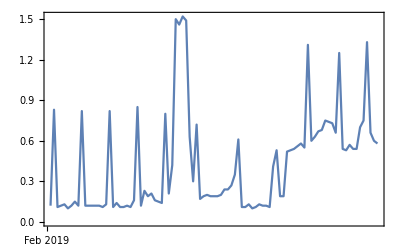
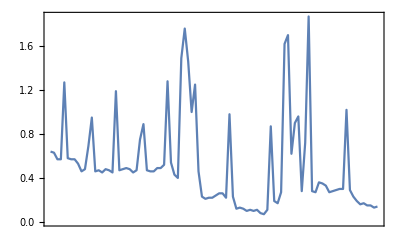
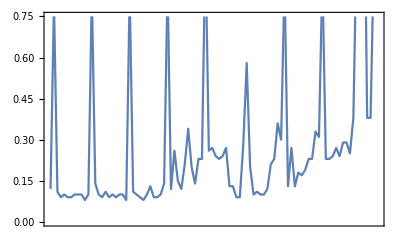
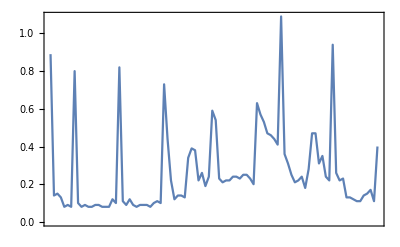
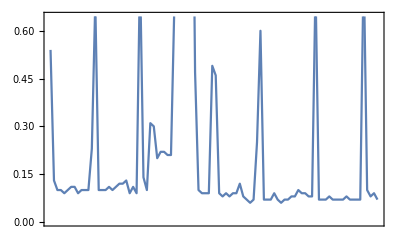
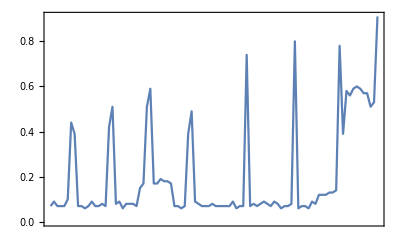
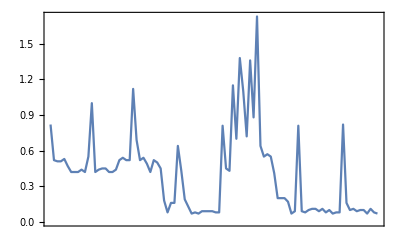
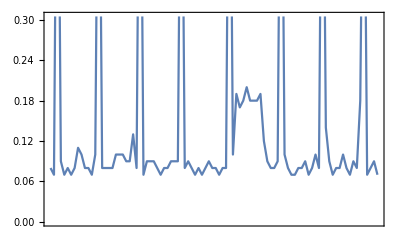
<|Day: Fri 1 Feb 2019→-Graphics-,Day: Sat 2 Feb 2019→-Graphics-,Day: Sun 3 Feb 2019→-Graphics-,Day: Mon 4 Feb 2019→-Graphics-,Day: Tue 5 Feb 2019→-Graphics-,Day: Wed 6 Feb 2019→-Graphics-,Day: Thu 7 Feb 2019→-Graphics-,Day: Fri 8 Feb 2019→-Graphics-,Day: Sat 9 Feb 2019→-Graphics-,Day: Sun 10 Feb 2019→-Graphics-,Day: Mon 11 Feb 2019→-Graphics-,Day: Tue 12 Feb 2019→-Graphics-,Day: Wed 13 Feb 2019→-Graphics-,Day: Thu 14 Feb 2019→-Graphics-,Day: Fri 15 Feb 2019→-Graphics-,Day: Sat 16 Feb 2019→-Graphics-,Day: Sun 17 Feb 2019→-Graphics-,Day: Mon 18 Feb 2019→-Graphics-,Day: Tue 19 Feb 2019→-Graphics-,Day: Wed 20 Feb 2019→-Graphics-,Day: Thu 21 Feb 2019→-Graphics-,Day: Fri 22 Feb 2019→-Graphics-,Day: Sat 23 Feb 2019→-Graphics-,Day: Sun 24 Feb 2019→-Graphics-,Day: Mon 25 Feb 2019→-Graphics-,Day: Tue 26 Feb 2019→-Graphics-,Day: Wed 27 Feb 2019→-Graphics-,Day: Thu 28 Feb 2019→-Graphics-,Day: Fri 1 Mar 2019→-Graphics-,Day: Sat 2 Mar 2019→-Graphics-,Day: Sun 3 Mar 2019→-Graphics-,Day: Mon 4 Mar 2019→-Graphics-,Day: Tue 5 Mar 2019→-Graphics-,Day: Wed 6 Mar 2019→-Graphics-,Day: Thu 7 Mar 2019→-Graphics-,Day: Fri 8 Mar 2019→-Graphics-,Day: Sat 9 Mar 2019→-Graphics-,Day: Sun 10 Mar 2019→-Graphics-,Day: Mon 11 Mar 2019→-Graphics-,Day: Tue 12 Mar 2019→-Graphics-,Day: Wed 13 Mar 2019→-Graphics-,Day: Thu 14 Mar 2019→-Graphics-,Day: Fri 15 Mar 2019→-Graphics-,Day: Sat 16 Mar 2019→-Graphics-,Day: Sun 17 Mar 2019→-Graphics-,Day: Mon 18 Mar 2019→-Graphics-,Day: Tue 19 Mar 2019→-Graphics-,Day: Wed 20 Mar 2019→-Graphics-,Day: Thu 21 Mar 2019→-Graphics-,Day: Fri 22 Mar 2019→-Graphics-,Day: Sat 23 Mar 2019→-Graphics-,Day: Sun 24 Mar 2019→-Graphics-,Day: Mon 25 Mar 2019→-Graphics-,Day: Tue 26 Mar 2019→-Graphics-,Day: Wed 27 Mar 2019→-Graphics-,Day: Thu 28 Mar 2019→-Graphics-,Day: Fri 29 Mar 2019→-Graphics-,Day: Sat 30 Mar 2019→-Graphics-,Day: Sun 31 Mar 2019→-Graphics-,Day: Mon 1 Apr 2019→-Graphics-,Day: Tue 2 Apr 2019→-Graphics-,Day: Wed 3 Apr 2019→-Graphics-,Day: Thu 4 Apr 2019→-Graphics-,Day: Fri 5 Apr 2019→-Graphics-,Day: Sat 6 Apr 2019→-Graphics-,Day: Sun 7 Apr 2019→-Graphics-,Day: Mon 8 Apr 2019→-Graphics-,Day: Tue 9 Apr 2019→-Graphics-,Day: Wed 10 Apr 2019→-Graphics-,Day: Thu 11 Apr 2019→-Graphics-,Day: Fri 12 Apr 2019→-Graphics-,Day: Sat 13 Apr 2019→-Graphics-,Day: Sun 14 Apr 2019→-Graphics-,Day: Mon 15 Apr 2019→-Graphics-,Day: Tue 16 Apr 2019→-Graphics-,Day: Wed 17 Apr 2019→-Graphics-,Day: Thu 18 Apr 2019→-Graphics-,Day: Fri 19 Apr 2019→-Graphics-,Day: Sat 20 Apr 2019→-Graphics-,Day: Sun 21 Apr 2019→-Graphics-,Day: Mon 22 Apr 2019→-Graphics-,Day: Tue 23 Apr 2019→-Graphics-,Day: Wed 24 Apr 2019→-Graphics-,Day: Thu 25 Apr 2019→-Graphics-,Day: Fri 26 Apr 2019→-Graphics-,Day: Sat 27 Apr 2019→-Graphics-,Day: Sun 28 Apr 2019→-Graphics-,Day: Mon 29 Apr 2019→-Graphics-,Day: Tue 30 Apr 2019→-Graphics-,Day: Wed 1 May 2019→-Graphics-,Day: Thu 2 May 2019→-Graphics-,Day: Fri 3 May 2019→-Graphics-,Day: Sat 4 May 2019→-Graphics-,Day: Sun 5 May 2019→-Graphics-,Day: Mon 6 May 2019→-Graphics-,Day: Tue 7 May 2019→-Graphics-,Day: Wed 8 May 2019→-Graphics-,Day: Thu 9 May 2019→-Graphics-,Day: Fri 10 May 2019→-Graphics-,Day: Sat 11 May 2019→-Graphics-,Day: Sun 12 May 2019→-Graphics-,Day: Mon 13 May 2019→-Graphics-,Day: Tue 14 May 2019→-Graphics-,Day: Wed 15 May 2019→-Graphics-,Day: Thu 16 May 2019→-Graphics-,Day: Fri 17 May 2019→-Graphics-,Day: Sat 18 May 2019→-Graphics-,Day: Sun 19 May 2019→-Graphics-,Day: Mon 20 May 2019→-Graphics-,Day: Tue 21 May 2019→-Graphics-,Day: Wed 22 May 2019→-Graphics-,Day: Thu 23 May 2019→-Graphics-,Day: Fri 24 May 2019→-Graphics-,Day: Sat 25 May 2019→-Graphics-,Day: Sun 26 May 2019→-Graphics-,Day: Mon 27 May 2019→-Graphics-,Day: Tue 28 May 2019→-Graphics-,Day: Wed 29 May 2019→-Graphics-,Day: Thu 30 May 2019→-Graphics-,Day: Fri 31 May 2019→-Graphics-,Day: Sat 1 Jun 2019→-Graphics-|>

```mathematica
regroupData[objects_] := DateListPlot[TimeSeries @ Map[
	{#["IntervalEnd"], #["Quantity"]} &,
	objects
]]


GroupBy[
	data, 
	toDate[#IntervalEnd] &,
	regroupData
]
```

```mathematica
Dataset[%]
```

Part::partd: Part specification Charting`ChartLabelingDump`dims⟦1⟧ is longer than depth of object.

Part::partd: Part specification Charting`ChartLabelingDump`dims⟦2⟧ is longer than depth of object.

Part::partd: Part specification Charting`ChartLabelingDump`dims⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

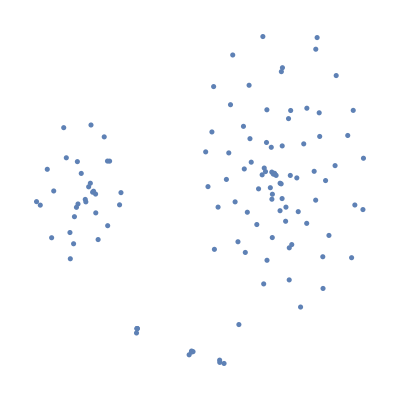

```mathematica
FeatureSpacePlot[%]
```

```mathematica
GroupBy[
	data, 
	toDate[#IntervalEnd] &, 
	Function[
		objects,
		TimeSeries @ Map[
			Function[
				{#IntervalEnd, #Quantity}
			],
			objects
		]
	]
]
```

```mathematica
time=data[All,"IntervalEnd"]//Normal;
usage=data[All,"Quantity"]//Normal ;
morganincrementAT=AssociationThread[time->usage];
morganincrementTS=TimeSeries[morganincrementAT];
```

```mathematica
morganmaster=TimeSeriesInsert[morganmaster,morganincrementTS]
```

```mathematica
data
```